KalloshとLinde (arXiv:hep-th/0411011) の仕事について、R-symmetryの観点からチェックしたい。
・実際、今考えているポテンシャルでもケーラーモジュライTはこの方針で固定しにいってる。
・ケーラーモジュライTのスケール的に、これが一番最初に固定されるはず。

F-termポテンシャルの計算

```mathematica
ClearAll;

zero[x_]=0;

W=w0+A Exp[-a T]+B Exp[-b T];
W̄=W/.{T->T̄};
K=-3Log[T+T̄];

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T};

vtemp=Exp[K]*((Subscript[K, T T̄])^(-1)*(DTW)*(OverBar[DTW])-3W*W̄);
Print["V=",vtemp];

V=FullSimplify@ComplexExpand[vtemp/.{T->ReT+I ImT,T̄->ReT-I ImT}];
Print["V=",V];
V=Expand[V/.{ImT->0,w0->-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0}];
Print["V=",V]; 
Print["W=",W/.{T->ReT+I ImT,T̄->ReT-I ImT}/.{ImT->0,w0->A (a A/(b B))^(a/(b-a))-B (a A/(b B))^(b/(b-a))+δw0}];
```

V=(-3 (A ⅇ^(-a T)+B ⅇ^(-b T)+w0) (A ⅇ^(-a T̄)+B ⅇ^(-b T̄)+w0)+1/3 (T+T̄)^2 (-a A ⅇ^(-a T)-b B ⅇ^(-b T)-(3 (A ⅇ^(-a T)+B ⅇ^(-b T)+w0))/(T+T̄)) (-a A ⅇ^(-a T̄)-b B ⅇ^(-b T̄)-(3 (A ⅇ^(-a T̄)+B ⅇ^(-b T̄)+w0))/(T+T̄)))/(T+T̄)^3

V=(ⅇ^(-2 (a+b) ReT) (a A^2 ⅇ^(2 b ReT) (3+a ReT)+b B^2 ⅇ^(2 a ReT) (3+b ReT)+ⅇ^((a+b) ReT) (3 a A ⅇ^(b ReT) w0 Cos[a ImT]+A B (3 (a+b)+2 a b ReT) Cos[(a-b) ImT]+3 b B ⅇ^(a ReT) w0 Cos[b ImT])))/(6 ReT^2)

V=(a A B ⅇ^(-((a+b) ReT)))/(2 ReT^2)+(A b B ⅇ^(-((a+b) ReT)))/(2 ReT^2)+(b B^2 ⅇ^(2 a ReT-2 (a+b) ReT))/(2 ReT^2)+(a A^2 ⅇ^(2 b ReT-2 (a+b) ReT))/(2 ReT^2)+(a A b B ⅇ^(-((a+b) ReT)))/(3 ReT)+(b^2 B^2 ⅇ^(2 a ReT-2 (a+b) ReT))/(6 ReT)+(a^2 A^2 ⅇ^(2 b ReT-2 (a+b) ReT))/(6 ReT)+(b B ⅇ^(a ReT-(a+b) ReT) δw0)/(2 ReT^2)+(a A ⅇ^(b ReT-(a+b) ReT) δw0)/(2 ReT^2)-(A b B ⅇ^(a ReT-(a+b) ReT) Abs[(a A)/(b B)]^(a/(-a+b)))/(2 ReT^2)-(a A^2 ⅇ^(b ReT-(a+b) ReT) Abs[(a A)/(b B)]^(a/(-a+b)))/(2 ReT^2)-(b B^2 ⅇ^(a ReT-(a+b) ReT) Abs[(a A)/(b B)]^(b/(-a+b)))/(2 ReT^2)-(a A B ⅇ^(b ReT-(a+b) ReT) Abs[(a A)/(b B)]^(b/(-a+b)))/(2 ReT^2)

W=A ((a A)/(b B))^(a/(-a+b))-((a A)/(b B))^(b/(-a+b)) B+A ⅇ^(-a ReT)+B ⅇ^(-b ReT)+δw0

パラメターをここでふる。今はW=w_0+A e^(-a T)+B e^(-b T)に対して、a=(2π)/100, b=(2π)/99として計算している。(このときw_0=-1.98×10^-4)

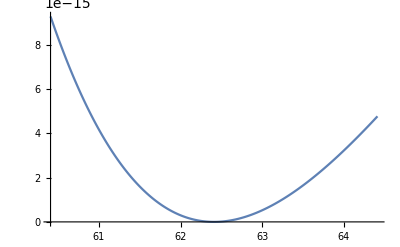

V_min=-1.48893×10^-28

<T>=62.4095

w_0=-1.98152×10^-4

W=0.

K=-14.4806

Ae^-aT=0.0198152

D_TW=3.85976×10^-16

```mathematica
Block[{$MaxExtraPrecision=Infinity},
valδw0=0;
vala=2Pi/100;
valb=2Pi/99;
valA=1;
valB=-1.03;

Quiet[
sol=FindMinimum[V*10^(10)/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0},{ReT,62},PrecisionGoal->Infinity,WorkingPrecision->MachinePrecision,MaxIterations->10000,Method->"Newton"];
];
valT=ReT/.sol[[2]];

range=2*10^(0);

Print[
Plot[V/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0},{ReT,valT-range,valT+range},WorkingPrecision->1000,PlotPoints->200]
];

Print["V_min=",N[sol[[1]]*10^(-15),3]];

Print["<T>=",N[valT,3]];
Print["w_0=",ScientificForm[-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}]];
Print["W=",N[W/.w0->-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.T->valT,3]];
Print["K=",N[K/.w0->-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.{T->valT,T̄->valT},3]];
];

Print["Ae^-aT=",N[A Exp[-a T]/.{A->valA,a->vala,T->valT},3]];
Print["D_TW=",N[DTW/.w0->-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.{T->valT,T̄->valT},3]];
```

a=(2π)/100+0.01, b=(2π)/99+0.01

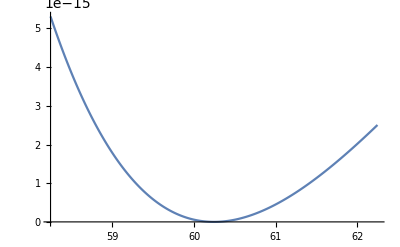

V_min=6.27×10^-24

<T>=60.24462987

w_0=-1.07372×10^-4

W=-8.67362×10^-18

K=-14.4

Ae^-aT=0.0124289

D_TW=-2.94579×10^-16

```mathematica
Δ=0.01;
Block[{$MaxExtraPrecision=Infinity},
valδw0=0;
vala=2Pi/100+Δ;
valb=2Pi/99+Δ;
valA=1;
valB=-1.03;

Quiet[
sol=FindMinimum[V*10^(10)/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0},{ReT,62},PrecisionGoal->Infinity,WorkingPrecision->10000,MaxIterations->10000,Method->"Newton"];
];
valT=ReT/.sol[[2]];

range=2*10^(0);

Print[
Plot[V/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0},{ReT,valT-range,valT+range},WorkingPrecision->1000,PlotPoints->200]
];

Print["V_min=",N[sol[[1]]*10^(-10),3]];

Print["<T>=",N[valT,10]];
Print["w_0=",ScientificForm[-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}]];
Print["W=",N[W/.w0->-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.T->valT,3]];
Print["K=",N[K/.w0->-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.{T->valT,T̄->valT},3]];
];

Print["Ae^-aT=",N[A Exp[-a T]/.{A->valA,a->vala,T->valT},3]];
Print["D_TW=",N[DTW/.w0->-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.{T->valT,T̄->valT},3]];
```

a=(2π)/100+0.01, b=(2π)/99+0.01, B=-1.028

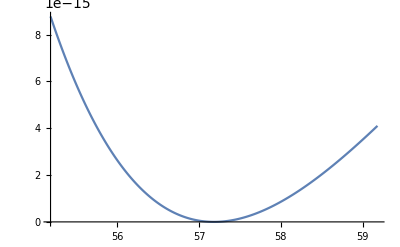

V_min=9.63×10^-24

<T>=57.18217228

w_0=-1.34201×10^-4

W=-1.73472×10^-18

K=-14.2

Ae^-aT=0.0155346

D_TW=-3.49501×10^-16

```mathematica
Δ=0.01;
Block[{$MaxExtraPrecision=Infinity},
valδw0=0;
vala=2Pi/100+Δ;
valb=2Pi/99+Δ;
valA=1;
valB=-1.028;

Quiet[
sol=FindMinimum[V*10^(10)/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0},{ReT,62},PrecisionGoal->Infinity,WorkingPrecision->10000,MaxIterations->10000,Method->"Newton"];
];
valT=ReT/.sol[[2]];

range=2*10^(0);

Print[
Plot[V/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0},{ReT,valT-range,valT+range},WorkingPrecision->1000,PlotPoints->200]
];

Print["V_min=",N[sol[[1]]*10^(-10),3]];

Print["<T>=",N[valT,10]];
Print["w_0=",ScientificForm[-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}]];
Print["W=",N[W/.w0->-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.T->valT,3]];
Print["K=",N[K/.w0->-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.{T->valT,T̄->valT},3]];
];

Print["Ae^-aT=",N[A Exp[-a T]/.{A->valA,a->vala,T->valT},3]];
Print["D_TW=",N[DTW/.w0->-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.{T->valT,T̄->valT},3]];
```

a=(2π)/100+1.0, b=(2π)/99+1.0

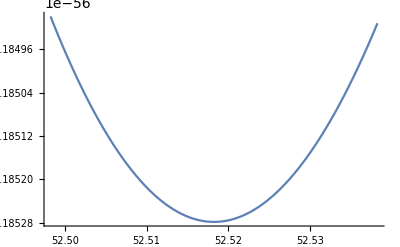

V_min=-1.19×10^-56

<T>=52.51824774

w_0=-6.98239×10^-26

W=-6.76643×10^-26

K=-14.

Ae^-aT=5.73485×10^-25

D_TW=-5.76444×10^-36

```mathematica
Δ=1.0;
Block[{$MaxExtraPrecision=Infinity},
valδw0=0;
vala=2Pi/100+Δ;
valb=2Pi/99+Δ;
valA=1.00;
valB=-1.03;

Quiet[
sol=FindMinimum[V*10^(10)/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0},{ReT,62},PrecisionGoal->Infinity,WorkingPrecision->10000,MaxIterations->10000,Method->"Newton"];
];
valT=ReT/.sol[[2]];

range=2*10^(-2);

Print[
Plot[V/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0},{ReT,valT-range,valT+range},WorkingPrecision->1000,PlotPoints->200]
];

Print["V_min=",N[sol[[1]]*10^(-10),3]];

Print["<T>=",N[valT,10]];
Print["w_0=",ScientificForm[-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}]];
Print["W=",N[W/.w0->-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.T->valT,3]];
Print["K=",N[K/.w0->-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.{T->valT,T̄->valT},3]];
];

Print["Ae^-aT=",N[A Exp[-a T]/.{A->valA,a->vala,T->valT},3]];
Print["D_TW=",N[DTW/.w0->-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.{T->valT,T̄->valT},3]];
```

a=(2π)/100+1.0, b=(2π)/99+1.0, A=1.0-0.05

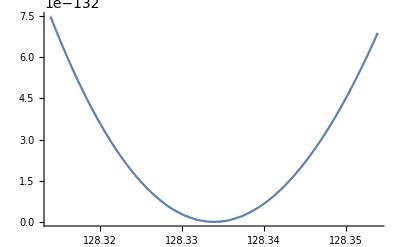

V_min=-2.59×10^-135

<T>=128.3339089

w_0=-3.28792×10^-63

W=6.63258×10^-75

K=-16.6

Ae^-aT=5.50935×10^-60

D_TW=5.7093×10^-70

```mathematica
Δ=1.0;
Block[{$MaxExtraPrecision=Infinity},
valδw0=0;
vala=2Pi/100+Δ;
valb=2Pi/99+Δ;
valA=1.00-0.05;
valB=-1.03;

Quiet[
sol=FindMinimum[V*10^(10)/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0},{ReT,62},PrecisionGoal->Infinity,WorkingPrecision->10000,MaxIterations->10000,Method->"Newton"];
];
valT=ReT/.sol[[2]];

range=2*10^(-2);

Print[
Plot[V/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0},{ReT,valT-range,valT+range},WorkingPrecision->1000,PlotPoints->200]
];

Print["V_min=",N[sol[[1]]*10^(-10),3]];

Print["<T>=",N[valT,10]];
Print["w_0=",ScientificForm[-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}]];
Print["W=",N[W/.w0->-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.T->valT,3]];
Print["K=",N[K/.w0->-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.{T->valT,T̄->valT},3]];
];

Print["Ae^-aT=",N[A Exp[-a T]/.{A->valA,a->vala,T->valT},3]];
Print["D_TW=",N[DTW/.w0->-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.{T->valT,T̄->valT},3]];
```

分かったこと：
基準として、W=w_0(a,b,A,B)+A^(-a T)+B e^(-b T)で、a=(2 π)/100, b=(2π)/99, A=1.00, B=-1.03をとって、そこからのズレで評価することを考える。
・まず、w_0の値はa,b->∞, A->0で0に近づいていく傾向がある。
  このとき、W->B^(-b T)となって、R対称性が回復する。
  また、この方向にパラメターを変化させていったときはT_VEV->∞で超対称な真空はランナウェイしていく傾向がある。
・Bの値をB->-∞にすると、上と同じ挙動を示す。

a=(2π)/100, b=(2π)/79
・Numerical errorか分からないので残しておく。

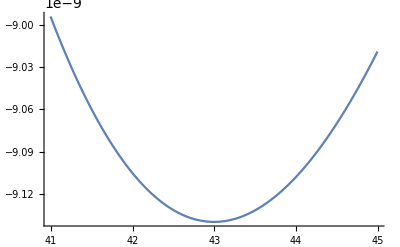

V_min=-9.14×10^-9

<T>=42.99525463

w_0=-7.74123×10^-2

W=-0.0440134

K=-13.4

Ae^-aT=0.0671

D_TW=-1.14925×10^-17

```mathematica
Δ=0;
Block[{$MaxExtraPrecision=Infinity},
valδw0=0;
vala=2Pi/100+Δ;
valb=2Pi/79+Δ;
valA=1;
valB=-1.03;

Quiet[
sol=FindMinimum[V*10^(10)/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0},{ReT,62},PrecisionGoal->Infinity,WorkingPrecision->10000,MaxIterations->10000,Method->"Newton"];
];
valT=ReT/.sol[[2]];

range=2*10^(0);

Print[
Plot[V/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0},{ReT,valT-range,valT+range},WorkingPrecision->1000,PlotPoints->200]
];

Print["V_min=",N[sol[[1]]*10^(-10),3]];

Print["<T>=",N[valT,10]];
Print["w_0=",ScientificForm[-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}]];
Print["W=",N[W/.w0->-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.T->valT,3]];
Print["K=",N[K/.w0->-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.{T->valT,T̄->valT},3]];
];

Print["Ae^-aT=",N[A Exp[-a T]/.{A->valA,a->vala,T->valT},3]];
Print["D_TW=",N[DTW/.w0->-A Abs[a A/(b B)]^(a/(b-a))-B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.{T->valT,T̄->valT},3]];
```